Parameters:

```mathematica
lambda = 515 (*nm*);
NA = 1.3;
```

Definition of radial distance in terms of wavelength and lens NA.

```mathematica
x[r_]:=2*π*NA*r/lambda
```

Conversion between integrated power and peak intensity

```mathematica
I0[P_]:=P*NA^2*π/lambda^2
```

```mathematica
Int[0, 30]
```

Int[0,30]

Intensity of Airy Ring as a function of radial distance from central spot (adding some non-zero offset)

```mathematica
Int[r_,P_]:= I0[P]*(2*BesselJ[1,x[r]]/(x[r]))^2 +0.01*I0[P]
```

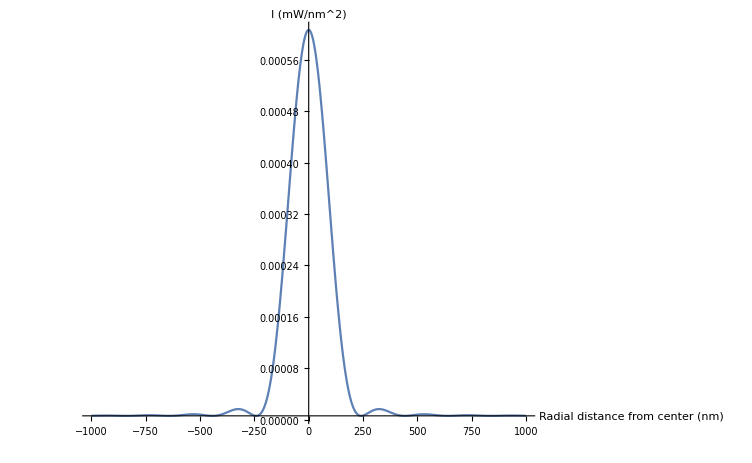

```mathematica
Plot[Int[r,30],{r,-1000 ,1000},PlotRange->Full, AxesLabel->{"Radial distance from center (nm)","I (mW/nm^2)"}]
```

Photo ionization rate of NV- to NV0 under red light, with proportionality factor ν

```mathematica
g1[ ν_, r_,P_] := ν*Int[r,P]^2
```

Percentage of population in NV-: e^-(ν1 I0^2 (2*J1(x)/x)^2 t)

```mathematica
η [ ν_,r_, t_,P_]:= Exp[-g1[ ν,r,P]*t]
```

Define rate factor and pulse time, and plot response from NV

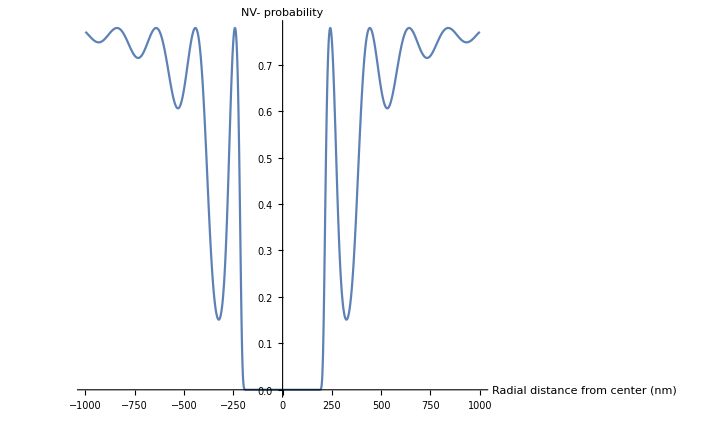

```mathematica
ν = 50 / (30 * NA^2 *π/lambda^2)^2; (* kHz nm^2 / mW*)
t = 50; (*ms*)
P=30; (*mW*)
p1=Plot[η [ ν,r, t ,P],{r,-1000, 1000},PlotRange->Full, AxesLabel->{"Radial distance from center (nm)","NV- probability"}];
p2=Plot[Exp[ν *t*I0[P]^2*(-4*BesselJ[2,3.8317]/3.8317*(x[r]-3.8317))^2],{r,-1000, 1000},PlotRange->Full,PlotStyle->{Red} ];
Show[p1, p2]
```

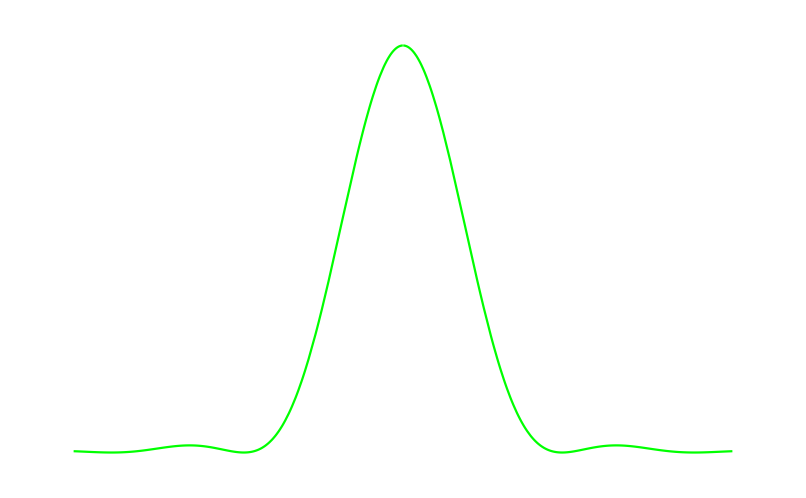

```mathematica
Plot[Int[r,30],{r,-500 ,500},PlotRange->Full, Axes->False, PlotStyle->Green]
```

```mathematica
RevolutionPlot3D[Int[r,10],{r, 0, 500}, PlotRange->Full, Mesh->None, PlotStyle->RGBColor[36/255,1,00, 0.9], Axes->False, Boxed->False]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Int[r,10],{r, 0, 500},  PlotRange->Full,Mesh->None, PlotStyle->RGBColor[1,226/255,00, 0.9], Axes->False, Boxed->False]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Int[r,10],{r, 0, 500},  PlotRange->Full,Mesh->None, PlotStyle->RGBColor[1,43/255,00, 0.9], Axes->False, Boxed->False]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Int[r,1],{r, 0, 500}, Mesh->None, PlotStyle->Green, Axes->False, Boxed->False]
```

-Graphics3D-